Bolhas em um cilindro na horizontal

```mathematica
Cilindro[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,π},{z,0,h},Mesh->None,PlotStyle->Directive[Opacity[1],Red],BoundaryStyle->Directive[Black,Thin],ViewPoint->{0,-∞,0},Lighting->{{"Ambient",Red}}]
```

```mathematica
Cilindro2[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,2π},{z,0,h},Mesh->None,PlotStyle->{Opacity[0.5],LightGray}]
```

## Testes

```mathematica
Bolhas[n_, raio_, h_] := 
(bubbles = {{},{}};
For[j=0,j<  n, j++;
rvalue= RandomReal[{0.1,2}];
Rzone= (raio-rvalue)*Sqrt[RandomReal[1]];
xvalue = Rzone Cos[θ];
yvalue = Rzone Sin[θ];
zvalue = RandomReal [{rvalue,h-rvalue}];

Which[rvalue ≥ 0.7,θ = RandomVariate[[BetaDistribution[9,9],(x+π)/(2*π)]],rvalue < 0.7 && rvalue≥ 0.3, θ =  RandomVariate[[BetaDistribution[4,4],(x+π)/(2*π)]],rvalue <0.3, θ =  RandomVariate[[BetaDistribution[2,2],(x+π)/(2*π)]]]

If[Length[bubbles⟦2⟧]==0, AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue];j=j+1];

touch={};
For[k=0,k< Length[bubbles⟦1⟧],k++;
pbubble = bubbles⟦1,k⟧;
rbubble = bubbles⟦2,k⟧;
Δx = xvalue - pbubble⟦1⟧;Δy = yvalue - pbubble⟦2⟧;Δz = zvalue - pbubble⟦3⟧;
If[√(Δx^2+Δy^2+Δz^2)> (rvalue + rbubble), AppendTo[touch,0], AppendTo[touch,1]]];

If[FreeQ[touch,1], AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue],j= j-1]];
AppendTo[bubbles,(Total[Table[4/3 π(bubbles⟦2,i⟧)^3,{i,1,Length[bubbles⟦2⟧]}]])];
AppendTo[bubbles,(Total[Table[π(bubbles⟦2,i⟧)^2,{i,1,Length[bubbles⟦2⟧]}]])];
bubbles)
```

```mathematica
VistaBolhas2D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];
Show[Graphics3D[{Opacity[1],Black,Sphere[bolhas⟦1⟧,bolhas⟦2⟧],ViewPoint->{0,- Infinity, 0}}],
Cilindro[r,h],Lighting->{{"Ambient",Red}},ViewPoint->{0,-∞,0}])
```

```mathematica
VistaBolhas3D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];Show[Graphics3D[{Opacity[0.5],Sphere[bolhas⟦1⟧,bolhas⟦2⟧]}],
Cilindro2[r,h]])
```

```mathematica
grafico [n0_,r0_,h0_]:=
(img=ColorSeparate[Image[VistaBolhas2D[n0,r0,h0],"Byte",ImageResolution->300]];
myLevels={ImageLevels[img⟦1⟧,2],ImageLevels[img⟦4⟧,2]};
vazio=1-N[myLevels[[1,2,2]]/myLevels[[2,2,2]]];
areareal= ((2*r0*h0) *vazio)/(2*r0)^2;
AppendTo[listaproj, {bubbles⟦3⟧/((2*r0)^3),areareal}];
listaproj);
```

```mathematica
GraficoExport[n0_,r0_,h0_]:=
(img=ColorSeparate[Image[VistaBolhas2D[n0,r0,h0],"Byte",ImageResolution->300]];
myLevels={ImageLevels[img⟦1⟧,2],ImageLevels[img⟦4⟧,2]};
vazio=1-N[myLevels[[1,2,2]]/myLevels[[2,2,2]]];
areareal= ((2*r0*h0) *vazio)/(2*r0)^2;
AppendTo[listaproj, {bubbles⟦3⟧/((2*r0)^3),areareal}];
listaproj);
```

```mathematica
PlotExport[n_,r_,h_,v_]:=
(lista3={};
listaproj={};

Do[lista3 = GraficoExport[n,r,h],{v}];
Export["700b_4x_horizontal",lista3,"CSV"]
);
```

## Produzindo gráficos

20b = 20 bolhas ; 4x = comprimento é 4 x o diâmetro do cilindro

```mathematica
PlotExport[20,9.5,76,200]
```

20b_4x_horizontal

```mathematica
PlotExport[100,9.5,76,200]
```

100b_4x_horizontal

```mathematica
PlotExport[200,9.5,76,200]
```

200b_4x_horizontal

```mathematica
PlotExport[50,9.5,76,200]
```

50b_4x_horizontal

```mathematica
PlotExport[150,9.5,76,200]
```

150b_4x_horizontal

```mathematica
PlotExport[300,9.5,76,200]
```

300b_4x_horizontal

```mathematica
PlotExport[20,9.5,95,200]
```

20b_5x_horizontal

```mathematica
PlotExport[100,9.5,95,200]
```

100b_5x_horizontal

```mathematica
PlotExport[200,9.5,95,200]
```

200b_5x_horizontal

```mathematica
PlotExport[400,9.5,76,200]
```

400b_4x_horizontal

```mathematica
PlotExport[500,9.5,76,200]
```

500b_4x_horizontal

```mathematica
PlotExport[600,9.5,76,200]
```

600b_4x_horizontal

```mathematica
PlotExport[700,9.5,76,200]
```

700b_4x_horizontal

## Rascunho

```mathematica
VistaBolhas3D[20,9.5,76]
```

-Graphics3D-

```mathematica
img1=ColorSeparate[Image[VistaBolhas2D[30,19,76],"Byte",ImageResolution->300]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

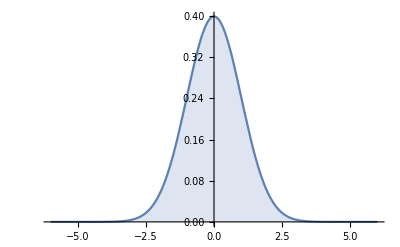

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{1}}]//Evaluate,{x,-6,6},Filling->Axis]
```